## Overlapping parallelograms with fixed areas. Figure: parrallelogramsFig1.eps

```mathematica
<<peeters` ;
peeters`setGitDir[ "../project/figures/GAelectrodynamics" ]
```

/Users/pjoot/project/figures/GAelectrodynamics

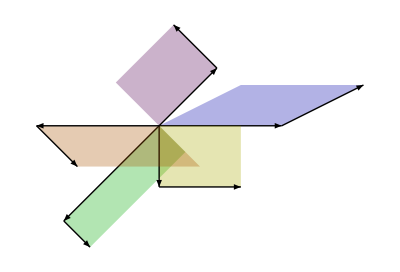

```mathematica
ClearAll[parrows, o, e1, e2, parallelogram,parrallelogramsFig1]
o = {0,0};
e1 = {1,0};
e2 = {0,1};
parallelogram[p_, {v1_, v2_}] := Polygon[{p+v1, p+v1+v2, p+v2, p}]
parrows[p_, {v1_, v2_}, c_] := {
Opacity[0.3],
parallelogram[p,{v1,v2}],
c,
Opacity[1],
Arrow[{p,v1}], Arrow[{p+v1,p + v1 + v2}]
};


p[c_] :=Module[{v1,v2,w1,w2,a},
v1 = 1.5 e1;
v2 = e1+ e2/2 ;
a=3/4;
w1 = -(e1+e2)/Sqrt[2];
w2 = (e1-e2)/Sqrt[2];
Graphics[ 
Flatten[
{
Opacity[0.3],
Blue // Darker,
parrows[o,{v1,v2}, c],
Green // Darker,
parrows[o,{2.2a w1,w2/2.2}, c],
Purple // Darker,
parrows[o,{- w1,-a w2}, c],
Yellow // Darker,
parrows[o,{-a e2, e1},c],
Orange // Darker,
parrows[o,{-v1 ,-v2+v1}, c]
},1]
]
]

parrallelogramsFig1  = p[Black]
```

```mathematica
peeters`exportForLatex["parrallelogramsFig1", parrallelogramsFig1]
```

{parrallelogramsFig1.eps,parrallelogramsFig1pn.png}